```mathematica
Quiet@Remove@"`*";ClearAll@"`*";
On[Assert]
SetDirectory[NotebookDirectory[]];

Row@{"Suffix: ",suffix="response"}
mcData=Import[StringJoin["mc-",suffix,".json"], "RawJSON"];
a1Data=Import[StringJoin["alg1-",suffix,".json"], "RawJSON"];
a2Data=Import[StringJoin["alg2-",suffix,".json"], "RawJSON"];


label[sample_Association,labels_]:=Block[{keys=Keys@sample,result},
result=sample;{"Mc","Alg1", "Alg2", "Theory"}
If[!MemberQ[keys,#],result[#]=0]&/@labels;
result
]
```

Suffix: response

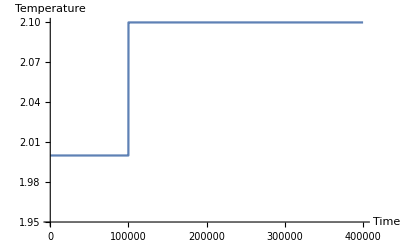

-Graphics-

```mathematica
{engyMc, engyAlg1, engyAlg2} = #["Energy difference"] &/@ {mcData, a1Data, a2Data};
T0 = mcData["T0"];
T = mcData["T"];
Assert@And ={
T0 == #["T0"] &/@{a1Data, a2Data},
T == #["T"]  &/@{a1Data, a2Data}};
time = Length[engyMc];
timeT0 = Divide[mcData["length temperature T0"], mcData["frame_step temperature T0"]] ;
Assert@And ={
time == Length[#]&/@{engyAlg1, engyAlg2},
timeT0 == Divide[#["length temperature T0"], #["frame_step temperature T0"]] &/@{a1Data, a2Data}};

temperaturePlot = Plot[Piecewise[{{T0,x<timeT0},{T,x>timeT0}}],{x,0,time}, AxesLabel->{"Time", "Temperature"}, PlotRange->{Automatic,  {1.95, 2.1}}]
ListLinePlot[{engyMc, engyAlg1, engyAlg2}, AxesLabel->{"Time", "Energy"}, PlotLegends->{"MC", "A1", "A2"}, PlotRange->{{100000, 100500}, Automatic}]
```